What is the terminal velocity of a SmartDart?

### from videos you can measure the length of the dart, and compare posiiton in 2 frames

```mathematica
AreaProj =π (0.06/2)^2 ;(*area of the dart, m^2, 60mm in diameter*)
Cd = 0.1; (*0.47 for sphere, 0.04 for streamlined body*)
m = 0.2; (*kg*)
ρ = 1.225; (*kg/m3*)
g= 9.8; (*m/s2*)
```

```mathematica
Vt =√((2 m g)/(ρ AreaProj Cd)) (*m/s*)
```

106.385

```mathematica
SDaccel[t_] := 2 m g - SDvel[t]^2 ρ AreaProj Cd
SDvel[t_] := ∫_0^t SDaccel[τ]ⅆτ
```

```mathematica
DSolve[{v'[t]==b - v[t]^2 a,v[0]==0},v,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
{{v->Function[{t},(√b Tanh[√a √b t])/(√a)]}}
```

Flling object reaches 90% speed at time

```mathematica
Solve[Tanh[√a √b t]==9/10,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→ArcTanh[9/10]/(√a √b)}}

Flling object reaches 90% speed when it falls from what height?

```mathematica
Solve[Tanh[√a √b t]==9/10,t]
```

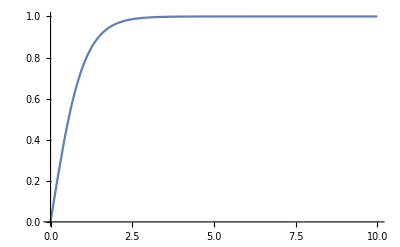

```mathematica
Plot[ Tanh[ t],{t,0,10},PlotRange->All]
```

```mathematica
DSolve[{v'[t]==2 m g - v[t]^2 ρ AreaProj Cd,v[0]==0},v,t]
```

$Aborted

```mathematica
s=NDSolve[{y''[t]==2 m g - y'[t]^2 ρ AreaProj Cd,y[0]==0,y'[0]==0},y,{t,0,100}]
```

{{y→InterpolatingFunction[{{0., 100.}}, <>]}}

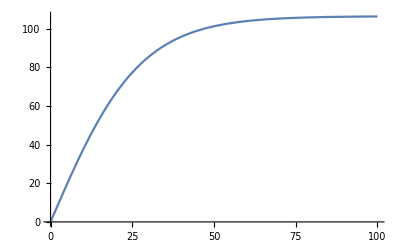

```mathematica
Plot[Evaluate[y'[t]/.s],{t,0,100},PlotRange->All]
```

```mathematica
Plot[SDvel[t],{t,0,10}]
```

$RecursionLimit::reclim: Recursion depth of 1024 exceeded.

General::stop: Further output of $RecursionLimit :: reclim will be suppressed during this calculation.

-Graphics-